# Hands-On Introduction to the Wolfram Physics Project

This computational essay is intended to help you get started exploring Wolfram models.  

This document is a notebook.  You can run it directly in the cloud by making your own copy, or you can download it to the desktop for use with any Wolfram Language system (e.g. Wolfram|One, Mathematica,  Wolfram Programming Lab, or Free Wolfram Engine for Developers).

Once you have your own copy of this notebook, you can edit any input, then evaluate it using ⇧+⌤.

You’ll see many objects here that look like .  These are functions that are automatically accessed from the Wolfram Function Repository.  To use them, either copy  etc. or type ResourceFunction[“WolframModel”] etc. 

 For a full list of functions related to the Wolfram Physics Project, see the List of Functions:

Click the + in   to get to documentation. Each function has extensive examples, that go much further than this document.

Note that in the Technical Introduction and Announcement all images are clickable, and provide code that can immediately be run in any Wolfram Language system:

The Registry of Notable Universes also contains a notebook for each universe.  All code in the notebook can be copied and run.

## Your First Universe

Let’s start by looking at a few steps of evolution for a particular rule.

Evolve for 5 steps from a self-loop:

```mathematica
[{{x,y},{x,z}}->{{x,z},{x,w},{y,w},{z,w}},{{0,0},{0,0}},5,"StatesPlotsList"]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

(Note that the very first time you run a Wolfram model function on your computer there may be a small delay while the necessary definitions are automatically downloaded and set up.)

The structures we’re getting here are representations of space in a very tiny universe.  We can make our universe slightly bigger by going 10 steps:

```mathematica
[{{x,y},{x,z}}->{{x,z},{x,w},{y,w},{z,w}},{{0,0},{0,0}},10,"FinalStatePlot"]
```

-Graphics-

Let’s take apart this example a little.

```mathematica
{{x,y},{x,z}}->{{x,z},{x,w},{y,w},{z,w}}
```

is the update rule we’re using.  We can make a graphic representation of the rule.

Make a graphical representation of the rule:

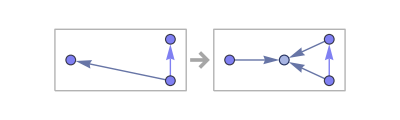

```mathematica
RulePlot[[{{x,y},{x,z}}->{{x,z},{x,w},{y,w},{z,w}}]]
```

The objects on which the rule operates are collections of “relations”, represented as lists of lists.

Give the state produced after 3 steps:

```mathematica
[{{x,y},{x,z}}->{{x,z},{x,w},{y,w},{z,w}},{{0,0},{0,0}},3,"FinalState"]
```

{{0,3},{1,3},{0,2},{0,4},{1,4},{2,4},{0,1},{0,5},{2,5},{1,5},{1,3},{1,6},{2,6},{3,6}}

We can represent these collections of relations as a hypergraph (or in this case a graph).

Generate a graph from a collection of relations:

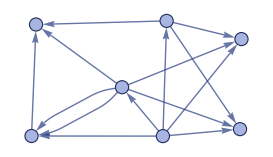

```mathematica
[{{0,3},{1,3},{0,2},{0,4},{1,4},{2,4},{0,1},{0,5},{2,5},{1,5},{1,3},{1,6},{2,6},{3,6}}]
```

Label the vertices:

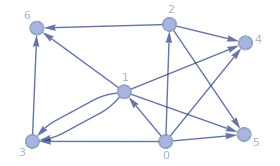

```mathematica
[{{0,3},{1,3},{0,2},{0,4},{1,4},{2,4},{0,1},{0,5},{2,5},{1,5},{1,3},{1,6},{2,6},{3,6}},VertexLabels->Automatic]
```

You can convert collections of relations to ordinary graphs, though if relations involve more than 2 elements, it won’t be a completely faithful conversion.

Convert to an ordinary graph:

```mathematica
[{{0,3},{1,3},{0,2},{0,4},{1,4},{2,4},{0,1},{0,5},{2,5},{1,5},{1,3},{1,6},{2,6},{3,6}}]
```

-Graphics-

Once you have an ordinary graph, you can use any of the many standard Wolfram Language graph functions.

Make a 3D rotatable version of a converted graph (the rule has been iconized to make the input simpler):

```mathematica
Graph3D[[[,{{0,0},{0,0}},10,"FinalState"]]]
```

-Graphics-

You can also try to reconstruct a 2D surface.

Try to putting “webbing” on the 3D graph, to form a 2D surface:

```mathematica
[[,{{0,0},{0,0}},10,"FinalState"]]
```

-Graphics-

You can make measurements on the states produced by Wolfram models.  As an example, you can compute the sizes of neighborhoods of successive larger radii around each element.

Compute the neighborhood volumes for each node:

```mathematica
[[,{{0,0},{0,0}},4,"FinalState"]]
```

<|0→{1,6,12},5→{1,5,11,12},1→{1,8,12},6→{1,4,12},2→{1,6,11,12},3→{1,6,11,12},7→{1,4,11,12},4→{1,5,11,12},8→{1,4,10,12},9→{1,4,12},10→{1,4,11,12},11→{1,4,12}|>

Compute the average over all nodes:

```mathematica
[Values[[[,{{0,0},{0,0}},10,"FinalState"]]]]
```

{1,5.000.07,14.840.20,31.80.4,57.60.8,93.41.3,140.31.9,197.32.6,261.53.1,326.23.3,384.52.9,429.02.2,458.61.3,474.50.7,480.820.31,482.730.10,483}

The flat part gives an estimate of effective dimension for the space corresponding to this state:

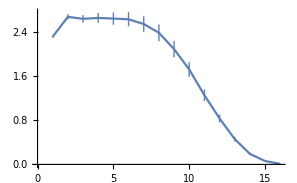

```mathematica
ListLinePlot[[%]]
```

## Symbolic Representation of Evolution

We just saw how one can get explicit states---or graphs---from .  But it is also possible to get a purely symbolic representation of the evolution, and indeed this is the default if you don’t ask for a specific property of  output.

If you don’t ask for a specific property, you get a symbolic evolution object:

```mathematica
[{{x,y},{x,z}}->{{x,z},{x,w},{y,w},{z,w}},{{0,0},{0,0}},10]
```

[…]

Set eo to be the evolution object:

```mathematica
eo=[{{x,y},{x,z}}->{{x,z},{x,w},{y,w},{z,w}},{{0,0},{0,0}},10];
```

Now you can ask for specific properties of the evolution object.  The complete list of possible properties is given in the documentation for WolframModelEvolutionObject.

VertexCountList gives a count of the number of vertices at each step:

```mathematica
eo["VertexCountList"]
```

{1,2,4,7,12,23,42,77,142,263,483}

A number gives a state; negative numbers count from the end of what has been computed:

```mathematica
eo[-7]
```

{{0,5},{1,6},{2,6},{3,6},{0,2},{0,7},{3,7},{2,7},{1,4},{1,8},{3,8},{4,8},{0,1},{0,9},{4,9},{1,9},{2,5},{2,10},{4,10},{5,10},{1,3},{1,11},{5,11},{3,11}}

There are other properties that can be computed from the evolution object.  One example is causal graphs.

Compute the causal graph for the evolution from the evolution object:

```mathematica
eo["CausalGraph"]
```

-Graphics-

If we want to have a better sense of how the causal graph could be laid out in time, we can make a layered causal graph.  In this case, however, the default graph layout is not so helpful.

Compute the layered causal graph:

```mathematica
eo["LayeredCausalGraph"]
```

-Graphics-

You can give graph options to determine the layout:

```mathematica
eo["LayeredCausalGraph",AspectRatio->1/2]
```

-Graphics-

## Multiway Systems

WolframModel normally shows you the state obtained after each “complete generation” of evolution.

Show evolution for 3 “generations”:

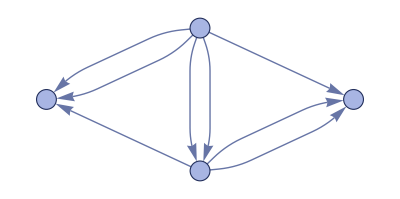
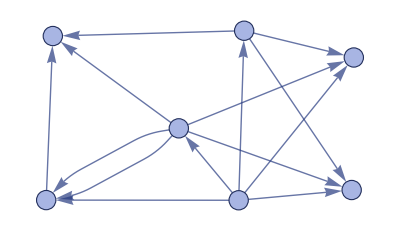
{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
[{{x,y},{x,z}}->{{x,z},{x,w},{y,w},{z,w}},{{0,0},{0,0}},3,"StatesPlotsList"]
```

You can also look at the effect of each individual updating event.  After the first generation, there are several involved in each generation.

Display each individual updating event in the evolution:

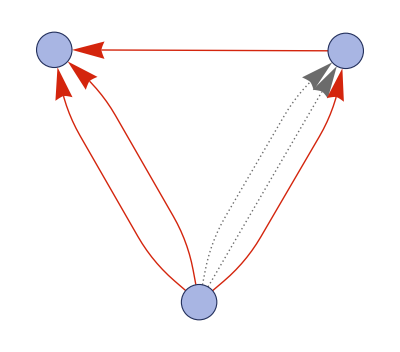
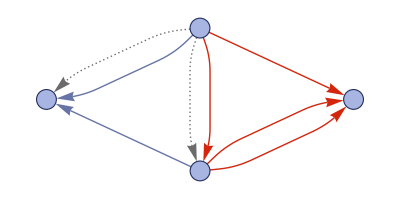
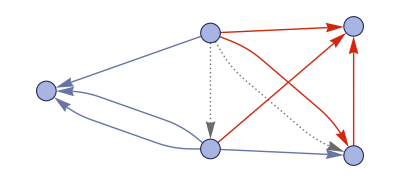
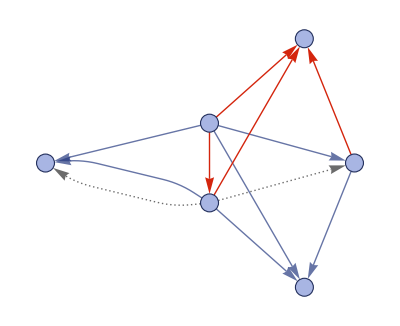
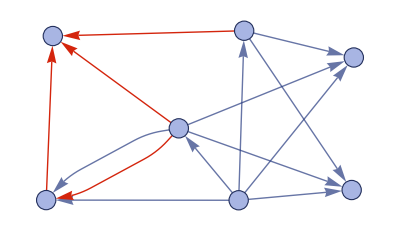
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
[,{{0,0},{0,0}},3,"EventsStatesPlotsList"]
```

A multiway system takes account of the different possible updating events that can be applied at each step.  The presence of multiple possible paths is a core feature of quantum mechanics.

Multiway systems quickly get large and difficult to render.

Show a multiway states+events graph, in which possible states are connected by possible events:

```mathematica
LayeredGraphPlot[[[],{{0,0},{0,0}},2,"EvolutionEventsGraph"],VertexSize->1]
```

-Graphics-

Show the states only:

```mathematica
LayeredGraphPlot[[[],{{0,0},{0,0}},2,"StatesGraph"],VertexSize->1]
```

-Graphics-

Show only the “structure” of the multiway graph, without showing the actual states:

```mathematica
LayeredGraphPlot[[[],{{0,0},{0,0}},2,"StatesGraphStructure"]]
```

-Graphics-

Even continuing for one more step can be somewhat time consuming:

```mathematica
LayeredGraphPlot[[[],{{0,0},{0,0}},3,"StatesGraphStructure"]]
```

-Graphics-

“Time” slices through the multiway graph give branchial graphs.  Branchial graphs are a representation of the entanglement of quantum states.

Compute the structure of the branchial graph at step 3:

```mathematica
[[],{{0,0},{0,0}},3,"BranchialGraphStructure"]
```

-Graphics-

It is also possible to look at causal connections between events in a multiway system.

Show causal connections between events:

```mathematica
LayeredGraphPlot[[[],{{0,0},{0,0}},2,"EvolutionCausalGraph"],VertexSize->1]
```

-Graphics-

The graph of all causal connections is the multiway causal graph.  We can show just this, without any explicit information about states.

Find the structure of the multiway causal graph:

```mathematica
[[],{{0,0},{0,0}},3,"CausalGraphStructure"]
```

-Graphics-

The multiway causal graph is represented just as an ordinary Wolfram Language graph, on which all standard operations can be done.

Simplify the graph by collapsing multiedges to single edges:

```mathematica
SimpleGraph[-Graphics-]
```

-Graphics-

Lay out the graph using spring-electrical embedding:

```mathematica
Graph[SimpleGraph[-Graphics-],GraphLayout->"SpringElectricalEmbedding"]
```

-Graphics-

## Hypergraphs

Whenever there are more than two elements in a relation, the collection of relations must be represented by a hypergraph rather than an ordinary graph.  In Wolfram models, the hypergraphs are always ordered, because elements in relations are ordered.

Generate a random ternary hypergraph:

```mathematica
[{10,{5,3}}]
```

{{5,10,1},{8,3,8},{5,9,7},{9,10,4},{8,6,9}}

WolframModelPlot renders hypergraphs.  Hyperedges are shown with “membranes”.

Render a hypergraph:

```mathematica
[{{5,10,1},{8,3,8},{5,9,7},{9,10,4},{8,6,9}}]
```

-Graphics-

Include automatic vertex labels:

```mathematica
[{{5,10,1},{8,3,8},{5,9,7},{9,10,4},{8,6,9}},VertexLabels->Automatic]
```

-Graphics-

One can define a canonical form for hypergraphs.  CanonicalHypergraph will convert any collection of relations to a canonical form.

Convert a hypergraph to canonical form by relabeling elements, and reordering:

```mathematica
[{{a,c,b},{b,d,a},{c,a,d}}]
```

{{1,2,3},{2,1,4},{3,4,1}}

The two hypergraphs are isomorphic, though they are not by default rendered the same:

```mathematica
/@{{{a,c,b},{b,d,a},{c,a,d}},{{1,2,3},{2,1,4},{3,4,1}}}
```

{-Graphics-,-Graphics-}

Explicitly check isomorphism:

```mathematica
[{{a,c,b},{b,d,a},{c,a,d}},{{1,2,3},{2,1,4},{3,4,1}}]
```

True

The “signature” of a hypergraph is the number of relations of a particular arity.  Given a particular signature, one can at least in principle enumerate all hypergraphs with that signature.

There are 5 possible canonical hypergraphs with a single 3-ary relation:

```mathematica
[{{1,3}}]
```

{{{1,1,1}},{{1,1,2}},{{1,2,1}},{{1,2,2}},{{1,2,3}}}

Render all the hypergraphs, with a “tiny” image for each:

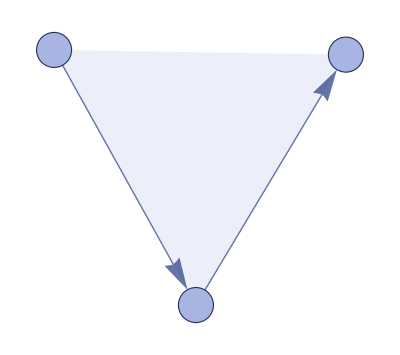
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
[#,ImageSize->Tiny]&/@[{{1,3}}]
```

There quickly start to be large numbers of possible hypergraphs for a given signature.

Find the number of 3-ary hypergraphs with 3 relations:

```mathematica
Length[[{{3,3}}]]
```

3268

You can use WolframModel to compute the evolution of rules based on transformations for hypergraphs that are not just ordinary graphs.  Note that if the rule involves only 3-ary relations, the initial condition must also include 3-ary relations.

Compute evolution for a rule involving 3-ary hypergraphs:

```mathematica
[{{x,x,y},{x,z,u}}->{{u,u,z},{y,v,z},{y,v,z}},{{0,0,0},{0,0,0}},5,"StatesPlotsList"]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Run this rule for 500 steps and a cone with 2D surface begins to emerge:

```mathematica
[{{x,x,y},{x,z,u}}->{{u,u,z},{y,v,z},{y,v,z}},{{0,0,0},{0,0,0}},500,"FinalStatePlot"]
```

-Graphics-

In this particular case, the causal graph is quite similar to the spatial hypergraph:

```mathematica
[{{x,x,y},{x,z,u}}->{{u,u,z},{y,v,z},{y,v,z}},{{0,0,0},{0,0,0}},500,"CausalGraph"]
```

-Graphics-

## Searching Rule Space

Just as one can enumerate possible hypergraphs, so also one can enumerate possible rules defining transformations between hypergraphs.  It is convenient to define a rule signature, which specifies the number of relations of particular arity on.

Format a signature corresponding to transforming a single ternary hyperedge to 4 ternary hyperedges:

```mathematica
[{{1,3}}->{{4,3}}]
```

1_3→4_3

There are typically very large numbers of ruleshttps://www.wolframphysics.org/technical-introduction/typical-behaviors/the-number-of-possible-rulesNonehttps://www.wolframphysics.org/technical-introduction/typical-behaviors/the-number-of-possible-rulesHyperlinkActionRecycledHyperlinkActive of any given signature.   But small cases can still be enumerated explicitly.  (Note that the enumeration functions will automatically use any parallel kernels set up on your computer system.)

Enumerate 1_2→1_2 rules:

```mathematica
[{{1,2}}->{{1,2}}]
```

{{{1,1}}→{{1,1}},{{1,1}}→{{1,2}},{{1,1}}→{{2,1}},{{1,2}}→{{1,1}},{{1,2}}→{{1,2}},{{1,2}}→{{2,1}},{{1,2}}→{{2,2}},{{1,2}}→{{1,3}},{{1,2}}→{{2,3}},{{1,2}}→{{3,1}},{{1,2}}→{{3,2}}}

The left and right-hand sides of Wolfram model rules are specified by hypergraphs.  But to make it clearer that the elements in these hypergraphs are intended to be “patterns” that can match any element in the spatial hypergraph it is often better to indicate them not by numbers but by letters.   has a conventionhttps://www.wolframphysics.org/technical-introductionNonehttps://www.wolframphysics.org/technical-introductionHyperlinkActionRecycledHyperlinkActive for doing this.

Give a rule in conventional “x,y” form:

```mathematica
[{{1,2,2},{3,1,4}}->{{2,5,2},{2,3,5},{4,5,5}}]
```

{{x,y,y},{z,x,u}}→{{y,v,y},{y,z,v},{u,v,v}}

Just as for hypergraphs, there are many possible forms for any given rule.    gives a canonical form.

Find the canonical form for a Wolfram model rule:

```mathematica
[{{1,2,a},{2,a,1}}->{{a,a,2},{1,2,3},{a,3,3}}]
```

{{1,2,3},{2,3,1}}→{{3,3,2},{3,4,4},{1,2,4}}

A convenient way to get Wolfram model rules to explore is to sample randomly from rules with a given signature.

Generate a random rule with a given signature:

```mathematica
[{{2,2}}->{{5,2}}]
```

{{1,2},{2,3}}→{{1,4},{1,5},{4,2},{6,4},{3,7}}

Randomly selected rules can have a huge range of possible behaviors.  One approach is just to try running for a very small number of steps.  Note that Automatic given as the initial condition yields a minimal self-loop necessary for the rule to apply.

Run for 3 steps (an initial condition of Automatic yields the minimal self-loop):

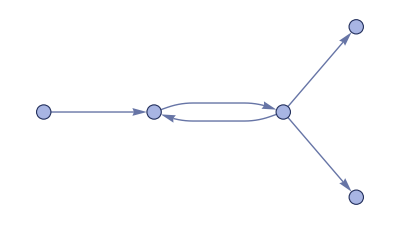
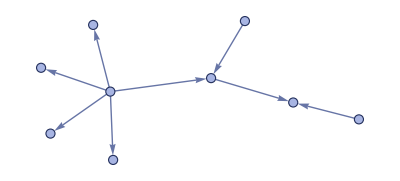
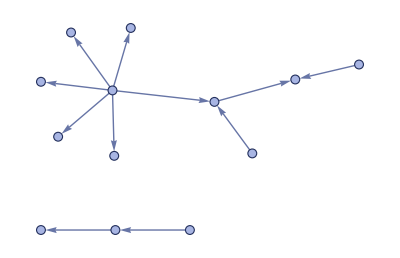
{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
[{{1,2},{2,3}}->{{1,4},{1,5},{4,2},{6,4},{3,7}},Automatic,3,"StatesPlotsList"]
```

The final spatial hypergraph here is disconnected, so physically contains causally independent regions of space.  You can check for disconnections in hypergraphs using .

Find the final hypergraph from the previous evolution:

```mathematica
[{{1,2},{2,3}}->{{1,4},{1,5},{4,2},{6,4},{3,7}},Automatic,3,"FinalState"]
```

{{1,3},{4,2},{1,5},{1,7},{8,6},{1,9},{1,10},{1,11},{10,6},{12,10},{2,13}}

This hypergraph is not connected:

```mathematica
[%]
```

False

Randomly selected rules often yield hypergraphs that grow very quickly.  The growth can be in number of nodes, number of edges, degree of a node, etc.

Find the growth in the number of vertices:

```mathematica
[{{1,2},{2,3}}->{{1,4},{1,5},{4,2},{6,4},{3,7}},Automatic,15,"VertexCountList"]
```

{1,5,9,13,21,33,49,73,109,161,237,349,513,753,1105,1621}

It is fairly common for such growth to be generated by a linear recurrence:

```mathematica
FindLinearRecurrence[%]
```

{2,-1,1,-1}

```mathematica
[{{1,2},{2,3}}->{{1,4},{1,5},{4,2},{6,4},{3,7}},Automatic,15,"EdgeCountList"]
```

{2,5,8,11,17,26,38,56,83,122,179,263,386,566,830,1217}

To ensure an evolution will not get too big,   allows you specify various “termination criteria” (as well as supporting TimeConstraint).  If you specify Automatic as the “number of steps”, automatic termination criteria will be applied.

Run the rule with automatic termination criteria:

```mathematica
[{{1,2},{2,3}}->{{1,4},{1,5},{4,2},{6,4},{3,7}},Automatic,Automatic,"VertexCountList"]
```

{1,5,9,13,21,33,49,73,109,161,237}

Generate plots (detailed plot rendering options apply to the evolution object):

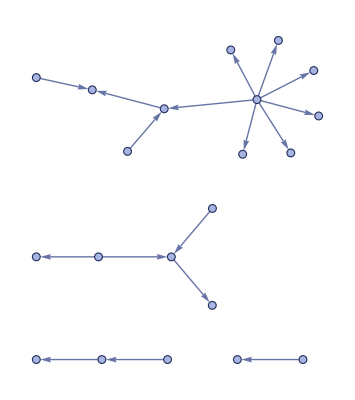
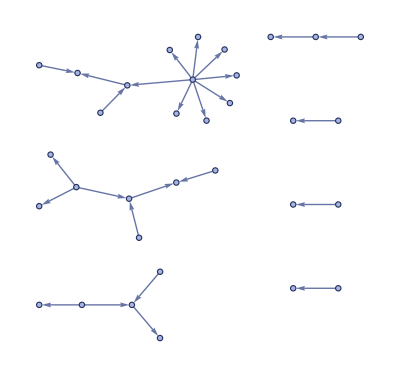
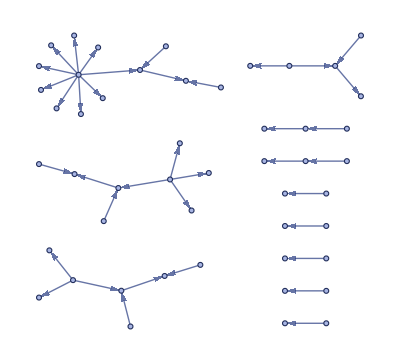
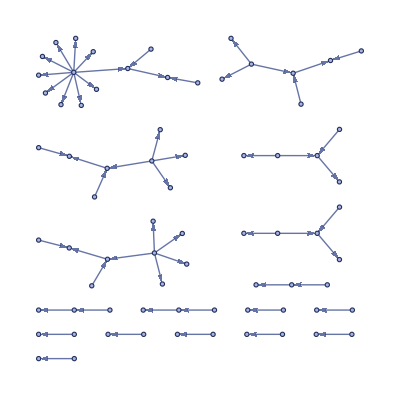
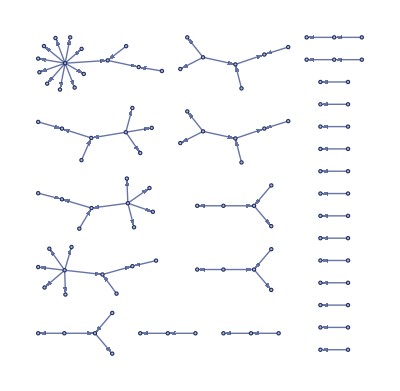
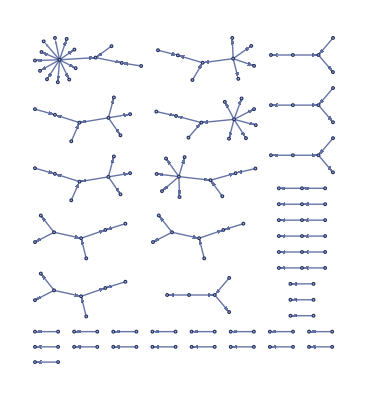
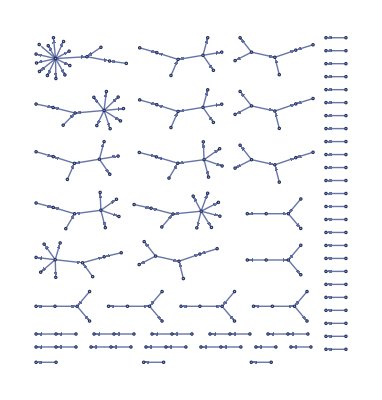
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
[{{1,2},{2,3}}->{{1,4},{1,5},{4,2},{6,4},{3,7}},Automatic,Automatic]["StatesPlotsList",ImageSize->Tiny]
```

A typical workflow is to generate a list of rules, then evolve each of them.  If you have multiple kernels available, this will be a good time to use them.  Often the rendering actually takes longer than the evolution.

Generate results for 10 randomly selected rules:

```mathematica
ParallelMap[[#,Automatic,Automatic]["FinalStatePlot",ImageSize->Tiny]&,Table[[{{2,2}}->{{5,2}}],10]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

You may want to apply a criterion to the outputs, for example checking if they are connected.  A convenient approach is first to generate a list of evolution objects.  You can test properties of the evolution object, then generate graphics, find the rule being used, etc.

Generate a list of evolution objects from evolving random rules:

```mathematica
eos=ParallelMap[[#,Automatic,Automatic]&,Table[[{{2,2}}->{{5,2}}],100]];
```

Select evolution objects where the final state is connected:

```mathematica
eosc=Select[eos,[#["FinalState"]]&];
```

Show results for rules where the last computed hypergraph is connected:

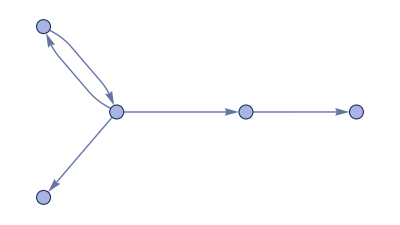
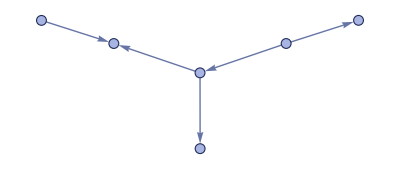
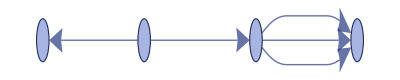
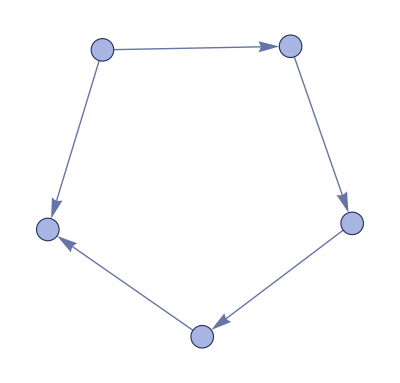
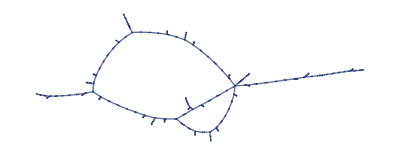
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
ParallelMap[#["FinalStatePlot",ImageSize->Tiny]&,eosc]
```

A common workflow is to generate many images of the behavior of rules, then visually select some of them.

Make a list of rules interactively selectable; Add adds the underlying rules for the case selected:

```mathematica
[ParallelMap[#["FinalStatePlot",ImageSize->Tiny]->#["Rules"]&,eosc]]
```

A complementary approach is to use machine learning. FeatureSapcePlot will arrange images in a feature space, allowing trends and outliers to be identified.

Make a feature space plot:

```mathematica
FeatureSpacePlot[ParallelMap[#["FinalStatePlot",ImageSize->Tiny]&,eosc]]
```

-Graphics-

When doing very large computations across many parallel systems, there are other considerations.   provides a good way to monitor progress.  There are often tradeoffs between parallelization of computation, and communications overhead.  One useful trick is to use Rasterize at a fairly low resolution on remotely generated images before sending them back to the master kernel.

## Rules from the Registry

The Registry of Notable Universes contains examples of rules that are deemed notable for one reason or another.  Each entry in the Registry has a short code, that can be used to retrieve the full rule.

Find a rule from the Registry using its short code:

```mathematica
["wm1433"]
```

{{{1,2},{1,3}}→{{2,4},{2,4},{2,1},{3,4}}}

Generate a plot of the final state, using automatic termination conditions for the evolution:

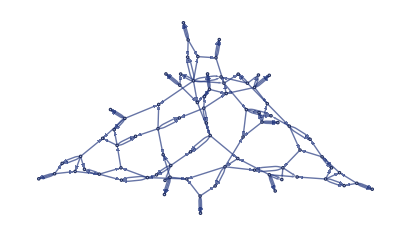

```mathematica
[["wm1433"],Automatic,Automatic,"FinalStatePlot"]
```

This shows the automatic evolution ran for 7 generations:

```mathematica
[["wm1433"],Automatic,Automatic,"GenerationsCount"]
```

{7,0}

This is what happens if one runs the same rule for 10 steps:

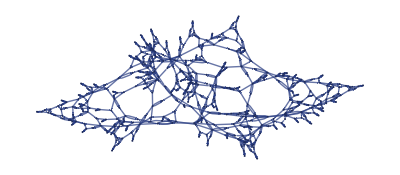

```mathematica
[["wm1433"],Automatic,10,"FinalStatePlot"]
```

It is possible to get a list of all rules in the Registry, from which one can then select rules with particular properties.

Show the first 10 rules from the Registry, sorted lexicographically:

```mathematica
Take[[],10]
```

{wm11114,wm1113,wm1116,wm1137,wm1157,wm1158,wm1167,wm1172,wm1173,wm1194}

Show results from evolving 5 randomly selected rules from the Registry:

```mathematica
[[#],Automatic,Automatic,"FinalStatePlot"]&/@RandomSample[[],5]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

## Graphs for Use as Examples

In understanding the principles of Wolfram models it is sometimes useful to look at simpler “model” graphs.

A 10×10 grid graph:

```mathematica
GridGraph[{10,10}]
```

-Graphics-

Grid graphs in successively higher dimensions:

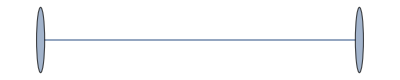
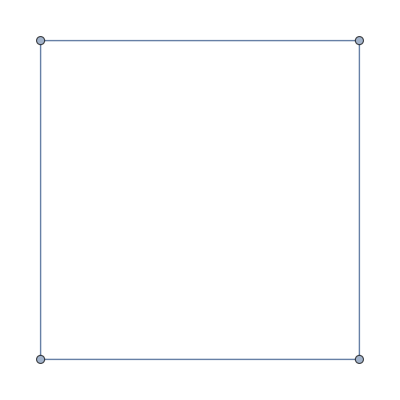
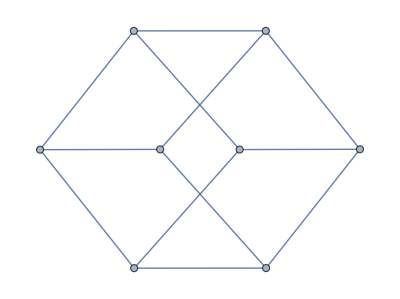
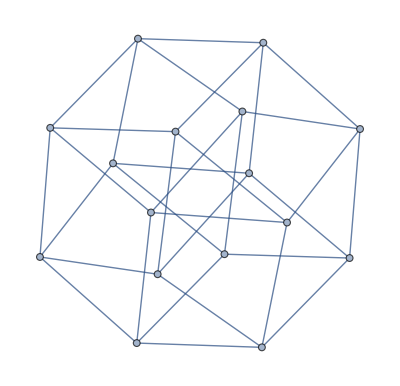
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[GridGraph[Table[2,d]],{d,5}]
```

The corresponding graphs rendered as 3D objects:

```mathematica
Table[Graph3D[GridGraph[Table[2,d]]],{d,5}]
```

-Graphics-

This produces a torus graph:

```mathematica
[{10,4}]
```

-Graphics-

The same operations can be done on these model graphs as on actual spatial hypergraphs from Wolfram models.

This computes the volumes of neighborhoods around a node in a torus graph:

```mathematica
First[Values[[[{20,8}]]]]
```

{1,5,13,25,40,56,72,88,104,120,135,147,155,159,160}

This plots a dimension estimate (the small size of the torus makes it deviate from 2):

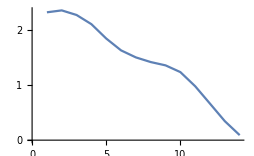

```mathematica
ListLinePlot[[%]]
```

There are various functions that construct other kinds of graphs that have obvious limits as continuous spaces.

Construct a hexagonal grid graph:

```mathematica
[{10,10}]
```

-Graphics-

A hexagonal torus graph:

```mathematica
[30,{2,5}]
```

-Graphics-

Construct a buckyball graph:

```mathematica
[2]
```

-Graphics-

This finds the shortest path in the graph between vertices 1 and 20:

```mathematica
FindShortestPath[[2],1,20]
```

{1,2,5,9,20}

Highlight this path:

```mathematica
HighlightGraph[[2],PathGraph[%]]
```

-Graphics-

Particularly for studying causal graphs, it is often convenient to have directed graphs as models.

Generate a 2D grid graph that is directed in one dimension but not the other:

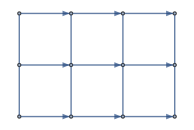

```mathematica
[{3,4->"Directed"}]
```

There are several built-in functions that are often useful in generating model graphs.

Generate a graph from a Menger sponge mesh:

```mathematica
MeshConnectivityGraph[MengerMesh[2,2]]
```

-Graphics-

Generate a graph from a meshing of a disk region:

```mathematica
MeshConnectivityGraph[DiscretizeRegion[Disk[]]]
```

-Graphics-

Generate a Cayley graph for a finite group:

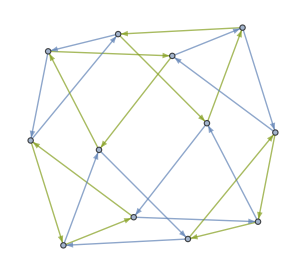

```mathematica
CayleyGraph[AlternatingGroup[4]]
```

For at least simple cases of infinite groups, CayleyNestGraph can be used:

```mathematica
[{{"i","j"},{"jij"->"i","iji"->"j"}},{""},10]
```

-Graphics-

## String Substitution Systems

In understanding Wolfram models, it is often convenient to consider the (typically simpler) case of string substitution systemshttps://www.wolframphysics.org/technical-introduction/the-updating-process-for-string-substitution-systemsNonehttps://www.wolframphysics.org/technical-introduction/the-updating-process-for-string-substitution-systemsHyperlinkActionRecycledHyperlinkActive.

The built-in SubstitutionSystem computes the evolution of a string substitution system using a particular updating order.

Compute a string substitution system evolution using a default updating order:

```mathematica
SubstitutionSystem[{"A"->"BBB","BB"->"A"},"A",10]
```

{A,BBB,AB,BBBB,AA,BBBBBB,AAA,BBBBBBBBB,AAAAB,BBBBBBBBBBBBB,AAAAAAB}

SubstitutionSystem does not keep track of causal relationship.   does this.

Generate substitution system evolution to keep track of causal relationships:

```mathematica
[{"A"->"BBB","BB"->"A"},"A",5]
```

{{A},{BBB,{{1,1}→{1,3}}},{AB,{{1,2}→{1,1}}},{BBBB,{{1,1}→{1,3}}},{AA,{{1,2}→{1,1},{3,4}→{2,2}}},{BBBBBB,{{1,1}→{1,3},{2,2}→{4,6}}}}

This shows the evolution with causal relationships included:

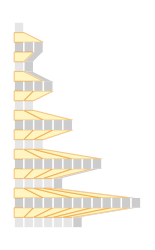

```mathematica
[[{"A"->"BBB","BB"->"A"},"A",10]]
```

It is also possible to directly generate a causal graph for string substitution system evolution.

Generate a causal graph for the evolution:

```mathematica
[{"A"->"BBB","BB"->"A"},"A",10]
```

-Graphics-

Just like with hypergraphs and Wolfram models, it is possible to enumerate strings and string substitution systemshttps://www.wolframphysics.org/technical-introduction/the-updating-process-for-string-substitution-systems/typical-multiway-graph-structuresNonehttps://www.wolframphysics.org/technical-introduction/the-updating-process-for-string-substitution-systems/typical-multiway-graph-structuresHyperlinkActionRecycledHyperlinkActive.

Construct all possible length-3 strings containing A, B and C:

```mathematica
["ABC",3]
```

{AAA,AAB,AAC,ABA,ABB,ABC,ACA,ACB,ACC,BAA,BAB,BAC,BBA,BBB,BBC,BCA,BCB,BCC,CAA,CAB,CAC,CBA,CBB,CBC,CCA,CCB,CCC}

Like Wolfram models, the structure of string substitution system rules can be specified by a signature, and one can then enumerate possible rules with a given signature.

Enumerate string substitution system rules with a particular signature, and 2 possible elements (A and B):

```mathematica
[{1->2,2->1},2]
```

{{A→AA,AA→A},{A→AA,AA→B},{A→AA,AB→A},{A→AA,AB→B},{A→AA,BB→A},{A→AA,BB→B},{A→AB,AA→A},{A→AB,AA→B},{A→AB,AB→A},{A→AB,AB→B},{A→AB,BA→A},{A→AB,BA→B},{A→AB,BB→A},{A→AB,BB→B},{A→BB,AA→A},{A→BB,AA→B},{A→BB,AB→A},{A→BB,AB→B},{A→BB,BB→A},{A→BB,BB→B}}

## Multiway String Substitution Systems

Compute successive collections of states in a multiway system:

```mathematica
[{"A"->"BBB","BB"->"A"},"A",6]
```

{{A},{BBB},{AB,BA},{BBBB},{ABB,BAB,BBA},{AA,BBBBB},{ABBB,BABB,BBAB,BBBA}}

Make the corresponding multiway states graph:

```mathematica
[{"A"->"BBB","BB"->"A"},"A",6,"StatesGraph"]
```

-Graphics-

Show only the structure of the multigraph graph:

```mathematica
[{"A"->"BBB","BB"->"A"},"A",10,"StatesGraphStructure"]
```

-Graphics-

Include the events:

```mathematica
[{"A"->"BBB","BB"->"A"},"A",6,"EvolutionEventsGraph"]
```

-Graphics-

Give only the structure:

```mathematica
[{"A"->"BBB","BB"->"A"},"A",6,"EvolutionEventsGraphStructure"]
```

-Graphics-

The (multiway) causal graph:

```mathematica
[{"A"->"BBB","BB"->"A"},"A",6,"CausalGraph"]
```

-Graphics-

Structure of the (multiway) causal graph:

```mathematica
[{"A"->"BBB","BB"->"A"},"A",6,"CausalGraphStructure"]
```

-Graphics-

All the graphs produced can be manipulated using standard Wolfram Language graph operations.

Use a different graph layout:

```mathematica
Graph[[{"A"->"BBB","BB"->"A"},"A",10,"CausalGraphStructure"],GraphLayout->"SpringElectricalEmbedding"]
```

-Graphics-

can also produce branchial graphs for string substitution systems.

Generate a branchial graph:

```mathematica
[{"A"->"BBB","BB"->"A"},"A",10,"BranchialGraph"]
```

-Graphics-

Show only the structure of the branchial graph:

```mathematica
[{"A"->"BBB","BB"->"A"},"A",15,"BranchialGraphStructure"]
```

-Graphics-

## Investigating Causal Invariance

Causal invariance is an important phenomenon that seems to lie at the heart of both relativity and quantum mechanics.  One can investigate causal invariance in the context of string substitution systems.

This generates the multiway graph for a particular causal-invariant rule:

```mathematica
[{"A"->"AB","B"->"A"},"A",4,"StatesGraph"]
```

-Graphics-

This gives a list of all branch pairs up to step 4:

```mathematica
[{"A"->"AB","B"->"A"},"A",4,"BranchPairsList"]
```

{{AA,ABB},{AAB,ABA},{AAB,ABBB},{ABA,ABBB},{AAA,AABB},{AAA,ABAB},{AABB,ABAB},{AAA,ABBA},{ABAB,ABBA},{AABB,ABBA},{AABB,ABBBB},{ABAB,ABBBB},{ABBA,ABBBB}}

Show the branchial graph for step 4:

```mathematica
[{"A"->"AB","B"->"A"},"A",4,"BranchialGraph"]
```

-Graphics-

This shows which branch pairs are resolved, or unresolved, at step 4:

```mathematica
[{"A"->"AB","B"->"A"},"A",4,"BranchPairResolutionsList"]
```

<|Resolved→{{AA,ABB},{AAB,ABA},{AAB,ABBB},{ABA,ABBB}},Unresolved→{{AAA,AABB},{AAA,ABAB},{AAA,ABBA},{AABB,ABAB},{AABB,ABBA},{AABB,ABBBB},{ABAB,ABBA},{ABAB,ABBBB},{ABBA,ABBBB}}|>

This rule can be verified as causal invariant:

```mathematica
[{"A"->"AB","B"->"A"},"A",4,"CausalInvariantQ"]
```

True

Causal invariance requires that all branch pairs resolve, but this can take an arbitrary number of steps.

Test a rule for causal invariance over a sequence of numbers of steps:

```mathematica
Table[[{"A"->"AA","AAB"->"BA"},"AAB",t,"CausalInvariantQ"],{t,5}]
```

{False,False,False,True,True}

Causal invariance can also be tested for Wolfram models.

Generate a multiway graph for a Wolfram model:

```mathematica
[[{{x,y}}->{{y,z},{z,x}}],{{0,0}},4,"StatesGraph",VertexSize->1]
```

-Graphics-

Generate a list of branch pairs:

```mathematica
[[{{x,y}}->{{y,z},{z,x}}],{{0,0}},4,"BranchPairsList"]
```

{{{{1,2},{1,3},{2,4},{4,3}},{{1,2},{2,3},{3,4},{4,1}}},{{{1,2},{2,3},{3,4},{4,5},{5,1}},{{1,2},{1,3},{2,4},{5,3},{5,4}}},{{{1,2},{2,3},{3,4},{4,5},{5,1}},{{1,2},{1,3},{2,4},{3,5},{4,5}}},{{{1,2},{1,3},{2,4},{5,3},{5,4}},{{1,2},{1,3},{2,4},{3,5},{4,5}}}}

Show the hypergraphs involved in the branch pairs:

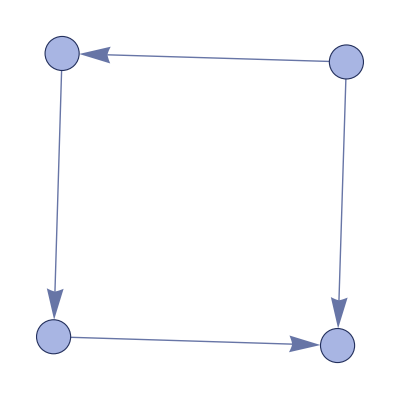
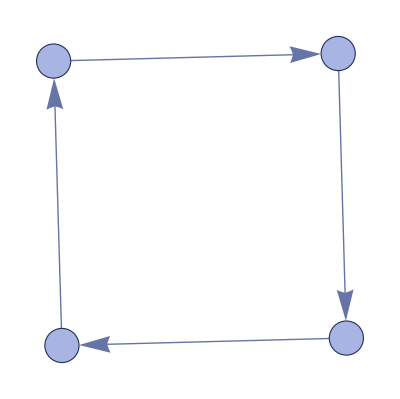
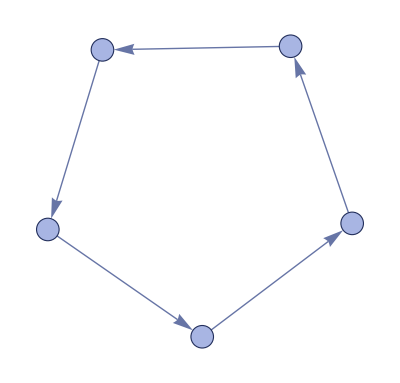
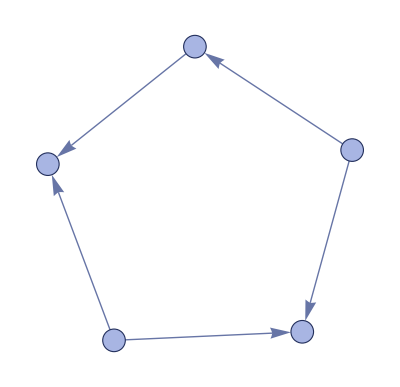
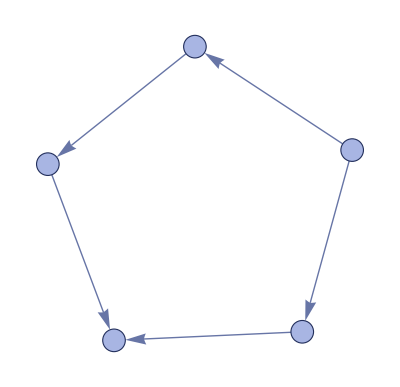
{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}}

```mathematica
Map[[#,ImageSize->Tiny]&,%,{2}]
```

Test the rule for causal invariance:

```mathematica
[[{{x,y}}->{{y,z},{z,x}}],{{0,0}},4,"CausalInvariantQ"]
```

True

## Using “Project Styles”

Particularly in keeping track of the various different kinds of graphs involved, the Wolfram Physics Project uses a specific set of designed styles.  You can access these using .

Here are the categories of styles:

```mathematica
Keys[ []]
```

{BranchialGraph,CausalGraph,EvolutionCausalGraph,EvolutionObject,GenericGraph,GenericLinePlot,Rule,RulialGraph,SpatialGraph,SpatialGraph3D,StatesGraph,StatesGraph3D}

These are styles defined for rulial graphs:

```mathematica
["RulialGraph"]
```

<|EdgeStyle→Hue[0.29, 0.97, 0.71],VertexIconBackground→Directive[Opacity[0.4],Hue[0.54, 0.41, 0.89]],VertexIconFontColor→Hue[0.62, 1, 0.48],VertexIconFrameMargins→{{2,2},{0,0}},VertexIconFrameStyle→Directive[Opacity[0.5],Hue[0.62, 0.52, 0.82]],VertexStyle→Directive[Hue[0.54, 0.41, 0.89],EdgeForm[Directive[Hue[0.63, 0.7, 0.33],Opacity[0.95]]]]|>

This makes a grid graph with rulial graph edge styles:

```mathematica
Graph[GridGraph[{5,5}],EdgeStyle->["RulialGraph","EdgeStyle"]]
```

-Graphics-

## Getting Help

Documentation for Wolfram Physics Project functions is available in the Wolfram Function Repository.

For official support contact Wolfram Research technical support.  The tools for the Wolfram Physics Project are considered supported functionality.

For informal support, post a message on the Wolfram Community.

## Tell Us What You Do!

We’re keen to know what you do with the tools we’ve built.

Please cite these tools as:
Wolfram Physics Project (2020), Wolfram Physics Project tools, wolframphysics.org/tools/.
It is also possible to cite individual functions, as in the Technical Introduction.

Please send us links to publications at wolframphysics-academic@wolfram.com so we can provide pointers on our website